# Reading diagrams from the book

## How a figure of Turaev & Virelizier becomes data that the CCN String Diagrams code can draw, type and simplify

By Dara O Shayda and Noor Hoshino (星野ヌール) · © Computational Classnotes · CC BY-NC-SA 4.0

The pictures in this notebook are crops of the book's pages, from Turaev & Virelizier, Monoidal Categories and Topological Field Theory (Progress in Mathematics 322, Springer 2017), © Springer International Publishing AG 2017. They are short excerpts, shown for study and commentary beside the book.

## 1. The method

No program reads the figures. A person (or any software or online service) looks at each figure, writes it down as data, and then lets the code check the transcription. Five steps:

1. Get the page as an image. Render the PDF page (pdftoppm, or Import with Rasterize) and crop the figure. The text around it comes from the PDF's text layer.

2. Read it from the bottom up, as the book draws it. The strands crossing the bottom edge are the source, read left to right. Then go up box by box: its name, which strands go in (counted from the left), which come out. Caps are ev, ẽv; cups are coev, c̃oev; crossings are τ, τ⁻271. In the pivotal calculus (§2.1.3) an arc pointing down is coloured X, an arc pointing up contributes X*.

3. Use the text. It says what each box is (f : X → Y, a pairing, a partition) and often gives the formula the figure stands for. That settles what the picture leaves open, such as the order of boxes at the same height.

4. Write it down: as editor text ("(id_X ⊗ ev_X)(coev_X ⊗ id_X)") or directly as a layered form LD[source, {{a, B[name, ins, outs]}, …}] listing the boxes bottom to top, a being the number of strands to the left of the box.

5. Check it. (a) It fits together: every box's inputs are the strands below it (validQ, and the type checker of expressionToLD). (b) It looks the same: draw it (render, renderP) beside the book's figure. (c) It computes the same: the rules take one side of the book's equation to the other (equationReport), and for the harder results the matrix models of the notebooks agree.

Most reading errors are in step 2: a crossing read the wrong way, an arrow missed, a box put on the wrong strand. Step 5 is there to catch them. Section 10 shows two such errors being caught.

## 2. Setup

Evaluate once. simplifier.wl loads expression-to-diagram.wl and diagram-to-expression.wl, and the rewriting engine. The helper bookAndOurs puts the book's picture beside our drawing.

```mathematica
Get[FileNameJoin[{$HomeDirectory, "Desktop", "Research", "Monoidal Graphical Calculus", "simplifier.wl"}]]
```

```mathematica
vee[text_, sig_] := expressionToLD[parseExpression[text], parseSignature[sig], "Duals" -> "vee"];
bookAndOurs[img_, lds_List, r_ : renderP] := Grid[{{img, Row[Riffle[Show[r[fromLayered[#]], ImageSize -> {UpTo[150], UpTo[120]}] & /@ lds, Style["  =  ", 16]]]}, {"the book", "our transcription"}}, Spacings -> {3, 1}, Alignment -> Center];
bookImage[name_String] := ToExpression[First[NotebookRead[First[Cells[EvaluationNotebook[], CellTags -> name]]]]]
```

## 3. Figure 2.1: level exchange (§2.1.1, p. 32)

-Graphics-

Figure 2.1 of the book. f : X → Y and g : U → V.

### Reading

Bottom edge: two strands, X then U. Top edge: Y then V. So all three pictures are morphisms X ⊗ U → Y ⊗ V.

Left picture: f on the first strand and g on the second, at the same height: f ⊗ g.

Middle: f is lower (on X), g higher (on U): first f ⊗ id_U, then id_Y ⊗ g, so (id_Y ⊗ g)(f ⊗ id_U).

Right: g first, then f: (f ⊗ id_V)(id_X ⊗ g). The text below the figure gives exactly these formulas.

### Transcription and checks

```mathematica
sig1 = "f : X → Y\ng : U → V";
fig21 = vee[#, sig1] & /@ {"f ⊗ g", "(id_Y ⊗ g)(f ⊗ id_U)", "(f ⊗ id_V)(id_X ⊗ g)"}
```

{LD[{X,U},{{0,B[f,{X},{Y}]},{1,B[g,{U},{V}]}}],LD[{X,U},{{0,B[f,{X},{Y}]},{1,B[g,{U},{V}]}}],LD[{X,U},{{1,B[g,{U},{V}]},{0,B[f,{X},{Y}]}}]}

The same, written by hand as layered forms (a = strands to the left of the box):

```mathematica
fig21 === {LD[{"X", "U"}, {{0, B["f", {"X"}, {"Y"}]}, {1, B["g", {"U"}, {"V"}]}}], LD[{"X", "U"}, {{0, B["f", {"X"}, {"Y"}]}, {1, B["g", {"U"}, {"V"}]}}], LD[{"X", "U"}, {{1, B["g", {"U"}, {"V"}]}, {0, B["f", {"X"}, {"Y"}]}}]}
```

True

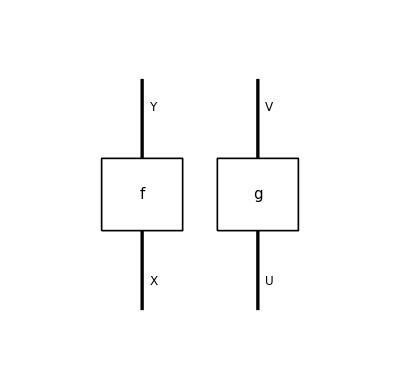
-Graphics- | -Graphics-  =  -Graphics-  =  -Graphics-
the book | our transcription

```mathematica
bookAndOurs[bookImage["fig2-1-level-exchange"], fig21, render]
```

Level exchange is not a rule: it is built into the normal form. All three have the same normal form, with no rewriting step at all:

```mathematica
{normalizeLD /@ fig21 // Apply[SameQ], equationReport["f ⊗ g = (id_Y ⊗ g)(f ⊗ id_U) = (f ⊗ id_V)(id_X ⊗ g)", sig1, "Duals" -> "vee"][[{"Steps", "Verdict"}]]}
```

{True,<|Steps→{{},{},{}},Verdict→✓ Both sides reduce to the same normal form, so the equation holds.|>}

## 4. The zigzag identities (2.1) (p. 32)

-Graphics-

(2.1): a pairing ω : X ⊗ Y → 𝟙 with inverse Ω : 𝟙 → Y ⊗ X.

### Reading

Left picture, bottom: one strand Y at the right; Ω (no inputs) at the bottom left. Ω puts out two strands: Y (it goes up the left side to the top) and X (it goes up into ω).

ω takes X (from Ω) and Y (the source strand), and puts out nothing. Top edge: Y. So it is the morphism Y → Y given by (id_Y ⊗ ω)(Ω ⊗ id_Y), and the picture says it equals id_Y.

Layer by layer: Ω at a = 0 on no strands; then ω at a = 1 on the strands X, Y. The right picture is the mirror image: (ω ⊗ id_X)(id_X ⊗ Ω) = id_X.

### Transcription and checks

```mathematica
zz = {LD[{"Y"}, {{0, B["Ω", {}, {"Y", "X"}]}, {1, B["ω", {"X", "Y"}, {}]}}], LD[{"X"}, {{1, B["Ω", {}, {"Y", "X"}]}, {0, B["ω", {"X", "Y"}, {}]}}]};
{validQ /@ zz, ldToExpression /@ zz}
```

{{True,True},{(id_Y⊗ω)∘(Ω⊗id_Y),(ω⊗id_X)∘(id_X⊗Ω)}}

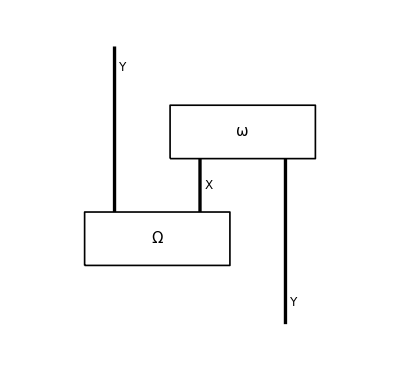
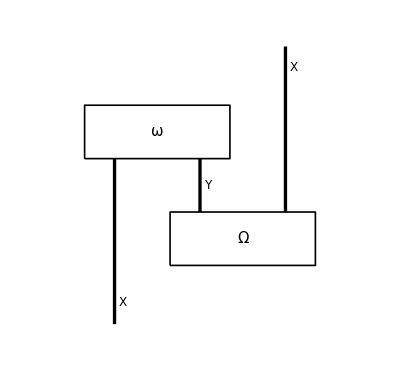
-Graphics- | -Graphics-  =  -Graphics-
the book | our transcription

```mathematica
bookAndOurs[bookImage["eq2-1-zigzag"], zz, render]
```

The rule (2.1) needs to know that (ω, Ω) is a pairing; the editor's signature line "pairing ω Ω" says the same:

```mathematica
simplifyLDTrace[#, "Duals" -> "vee", "Pairings" -> {{"ω", "Ω"}}][[All, 1]] & /@ zz
```

{{start,(2.1) left zigzag},{start,(2.1) right zigzag}}

## 5. The left dual ∨f (§2.1.2, p. 33)

-Graphics-

The definition of ∨f : ∨Y → ∨X for f : X → Y.

### Reading

Right side, bottom: one strand ∨Y at the left. coev_X (a box with no inputs) sits to its right and puts out X and ∨X.

f sits on the X strand (the second strand) and turns it into Y. ev_Y takes ∨Y and Y (strands 1 and 2) and closes them. What is left goes up on the right: ∨X.

So ∨f = (ev_Y ⊗ id_∨X)(id_∨Y ⊗ f ⊗ id_∨X)(id_∨Y ⊗ coev_X).

### Transcription and checks

```mathematica
vf = vee["(ev_Y ⊗ id_{∨X})(id_{∨Y} ⊗ f ⊗ id_{∨X})(id_{∨Y} ⊗ coev_X)", "f : X → Y"]
```

LD[{∨Y},{{1,B[coev_X,{},{X,∨X}]},{1,B[f,{X},{Y}]},{0,B[ev_Y,{∨Y,Y},{}]}}]

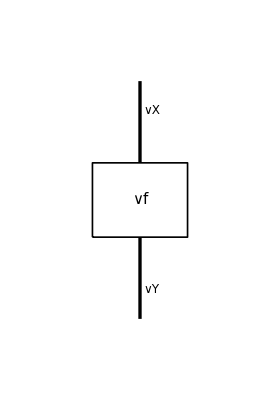
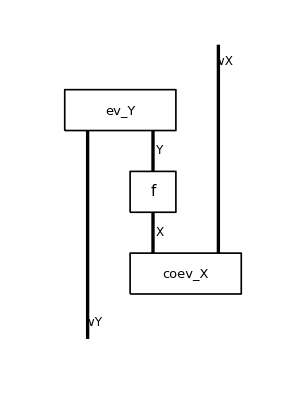
-Graphics- | -Graphics-  =  -Graphics-
the book | our transcription

```mathematica
bookAndOurs[bookImage["vee-f-definition"], {vee["∨f", "f : X → Y"], vf}, render]
```

```mathematica
simplifyLDTrace[vf, "Duals" -> "vee"] // Column
```

{start,LD[{∨Y},{{1,B[coev_X,{},{X,∨X}]},{1,B[f,{X},{Y}]},{0,B[ev_Y,{∨Y,Y},{}]}}]}
{definition of ∨f,LD[{∨Y},{{0,B[∨f,{∨Y},{∨X}]}}]}

## 6. Figure 2.2: duality identities with arrows (§2.1.3, p. 34)

-Graphics-

Figure 2.2. Arrows now carry the duals: an arc pointing down is X, an arc pointing up is X*.

### Reading

The key on the same page: ev_X and ẽv_X are caps, coev_X and c̃oev_X are cups; which is which is read from the arrow on the arc.

First picture: the source is the strand at the bottom right, pointing down, so X. It goes up into a cap on the right; the cap comes down into a cup on the left, which goes up to the top left. Bottom to top: the cup coev_X : 𝟙 → X ⊗ X* to the left of X, then the cap ev_X : X* ⊗ X → 𝟙 on strands 2, 3. So (id_X ⊗ ev_X)(coev_X ⊗ id_X) = id_X.

Third picture: the mirror image, with ẽv and c̃oev: (ẽv_X ⊗ id_X)(id_X ⊗ c̃oev_X) = id_X. The right half is the same with the arrows reversed, the identities of id_X*.

### Transcription and checks

```mathematica
fig22 = textToLD[#, "X"] & /@ {"(id_X ⊗ ev_X)(coev_X ⊗ id_X)", "id_X", "(ev~_X ⊗ id_X)(id_X ⊗ coev~_X)", "(ev_X ⊗ id_{X*})(id_{X*} ⊗ coev_X)", "id_{X*}", "(id_{X*} ⊗ ev~_X)(coev~_X ⊗ id_{X*})"}
```

{LD[{X},{{0,B[coev_X,{},{X,X*}]},{1,B[ev_X,{X*,X},{}]}}],LD[{X},{}],LD[{X},{{1,B[OverTilde[coev]_X,{},{X*,X}]},{0,B[OverTilde[ev]_X,{X,X*},{}]}}],LD[{X*},{{1,B[coev_X,{},{X,X*}]},{0,B[ev_X,{X*,X},{}]}}],LD[{X*},{}],LD[{X*},{{0,B[OverTilde[coev]_X,{},{X*,X}]},{1,B[OverTilde[ev]_X,{X,X*},{}]}}]}

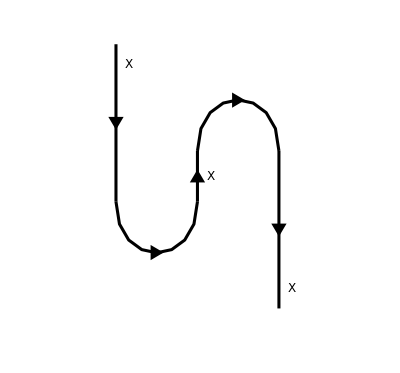
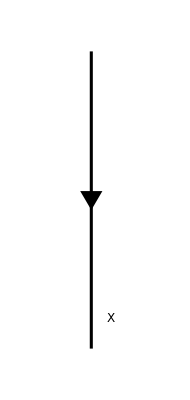
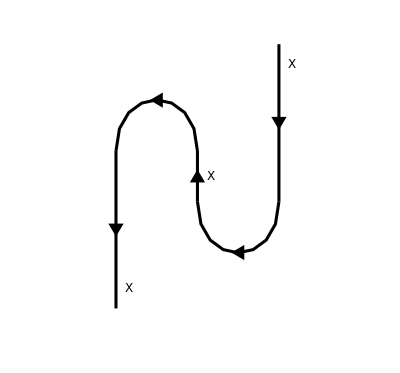
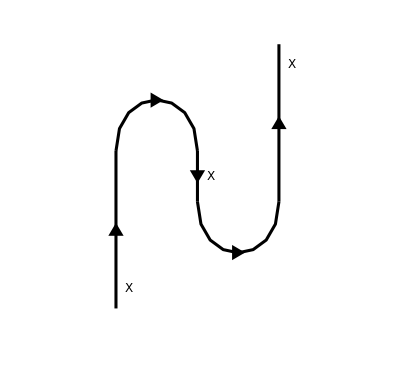
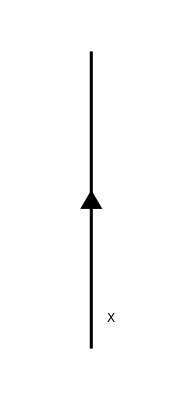
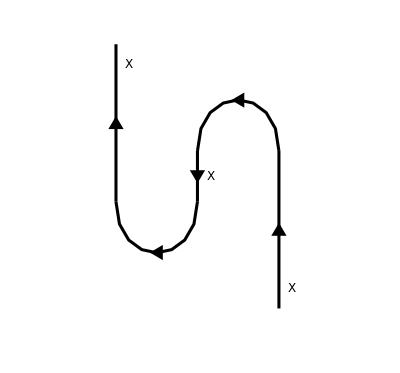
-Graphics- | -Graphics-  =  -Graphics-  =  -Graphics-  =  -Graphics-  =  -Graphics-  =  -Graphics-
the book | our transcription

```mathematica
bookAndOurs[bookImage["fig2-2-duality"], fig22]
```

```mathematica
{equationReport["(id_X ⊗ ev_X)(coev_X ⊗ id_X) = id_X = (ev~_X ⊗ id_X)(id_X ⊗ coev~_X)", "X"]["Steps"], equationReport["(ev_X ⊗ id_{X*})(id_{X*} ⊗ coev_X) = id_{X*} = (id_{X*} ⊗ ev~_X)(coev~_X ⊗ id_{X*})", "X"]["Holds"]}
```

{{{(2.1) left zigzag},{},{(2.1) right zigzag}},True}

## 7. Figure 2.3: the dual morphism f* (p. 34)

-Graphics-

Figure 2.3: two expressions for f* : Y* → X*.

### Reading

Left picture: the source strand at the bottom left points up and is labelled Y, so it is Y*. To its right a cup (no inputs) puts out X (pointing down, into f) and X* (pointing up, to the top right): coev_X.

f turns X into Y, and a cap closes Y* (the source) with Y: ev_Y. The strand left at the top is X*, pointing up. So f* = (ev_Y ⊗ id_X*)(id_Y* ⊗ f ⊗ id_X*)(id_Y* ⊗ coev_X).

Right picture: the mirror image, with ẽv_Y and c̃oev_X.

### Transcription and checks

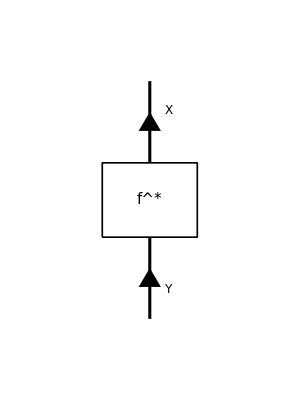
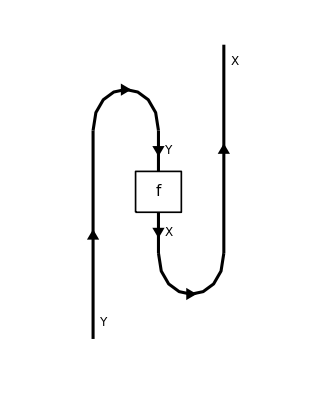
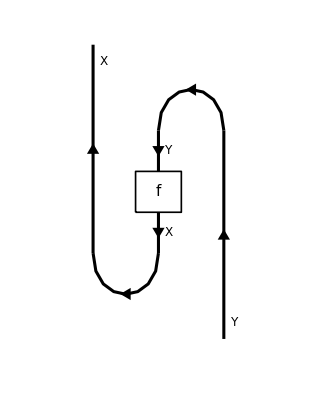
-Graphics- | -Graphics-  =  -Graphics-  =  -Graphics-
the book | our transcription

```mathematica
fs = textToLD[#, "f : X → Y"] & /@ {"f*", "(ev_Y ⊗ id_{X*})(id_{Y*} ⊗ f ⊗ id_{X*})(id_{Y*} ⊗ coev_X)", "(id_{X*} ⊗ ev~_Y)(id_{X*} ⊗ f ⊗ id_{Y*})(coev~_X ⊗ id_{Y*})"};
bookAndOurs[bookImage["fig2-3-dual-morphism"], fs]
```

```mathematica
equationReport["f* = (ev_Y ⊗ id_{X*})(id_{Y*} ⊗ f ⊗ id_{X*})(id_{Y*} ⊗ coev_X) = (id_{X*} ⊗ ev~_Y)(id_{X*} ⊗ f ⊗ id_{Y*})(coev~_X ⊗ id_{Y*})", "f : X → Y"][[{"Steps", "Verdict"}]]
```

<|Steps→{{},{Fig. 2.3 fold (left)},{Fig. 2.3 fold (right)}},Verdict→✓ Both sides reduce to the same normal form, so the equation holds.|>

## 8. The left twist θˡ (§3.3.1, p. 59)

-Graphics-

The left twist θˡ_X, drawn as a curl, with its formula.

### Reading

A curl is read like any other diagram once it is cut into pieces: at the bottom a cup on the left (c̃oev_X, putting out X* and X), then a crossing of the two X strands (τ_{X,X}, the strand going up to the right passes over), then a cap on the left (ev_X on X* and X).

Here the book also prints the formula, so the reading can be checked letter for letter: (ev_X ⊗ id_X)(id_X* ⊗ τ_{X,X})(c̃oev_X ⊗ id_X).

A crossing is the easiest thing to misread: over or under decides between τ_{X,X} (giving θˡ) and τ⁻271_{X,X} (giving the inverse of θʳ).

### Transcription and checks

```mathematica
curl = textToLD["(ev_X ⊗ id_X)(id_{X*} ⊗ τ_{X,X})(coev~_X ⊗ id_X)", "X"]
```

LD[{X},{{0,B[OverTilde[coev]_X,{},{X*,X}]},{1,B[τ_(X,X),{X,X},{X,X}]},{0,B[ev_X,{X*,X},{}]}}]

Our renderer draws the crossing τ_{X,X} as a box with two inputs and two outputs; the editor draws it as a crossing. The data is the same.

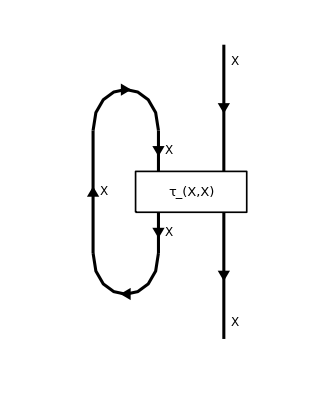
-Graphics- | -Graphics-
the book | our transcription

```mathematica
bookAndOurs[bookImage["theta-left-twist"], {curl}]
```

```mathematica
simplifyLDTrace[curl] // Column
```

{start,LD[{X},{{0,B[OverTilde[coev]_X,{},{X*,X}]},{1,B[τ_(X,X),{X,X},{X,X}]},{0,B[ev_X,{X*,X},{}]}}]}
{twist fold (§3.3.1),LD[{X},{{0,B[θˡ_X,{X},{X}]}}]}

## 9. Chapter 4: partitions (4.7) and (4.9) (p. 80)

-Graphics-

(4.7): for an i-partition (p_α, q_α) of X.

-Graphics-

(4.9): for a 1-partition (p_β, q_β) of X, with f : 𝟙 → X and g : X → 𝟙.

### Reading

The red shapes are the book's notation for a partition (§4.6.1): the semi-disk is p_α : X → i, the rectangle with a half-disk cut out is q_α : i → X. Here they are not boxes with names written in them, so the text decides which is which.

(4.7), bottom to top: i, then the rectangle q_α (i → X), then the semi-disk p_α (X → i), then i. So p_α q_α, and the picture says it is N^i_X id_i, the multiplicity of i in X.

(4.9), left: f : 𝟙 → X at the bottom, then p_β : X → 𝟙 (the semi-disk, with nothing above it since the target is 𝟙 and 𝟙 is not drawn), then q_β : 𝟙 → X. So q_β p_β f = f. The right equation is the same upside down: g q_β p_β = g.

In Chapter 4 a diagram is a term of a linear combination: a coefficient, sums, the partition pairs, and the layered form. The pairs say which boxes are p_α and q_α: "W" is the object partitioned and "t" the simple object.

### Transcription and checks

```mathematica
term47 = <|"c" -> <|"n" -> 1, "d" -> 1, "at" -> <||>|>, "sums" -> {}, "pairs" -> <|"α" -> <|"W" -> {"X"}, "t" -> "i"|>|>,
   "ld" -> LD[{"i"}, {{0, B["q_α", {"i"}, {"X"}]}, {0, B["p_α", {"X"}, {"i"}]}}]|>;
simplifyTermTrace[term47, "Simples" -> {"i"}] // Column
```

{start,<|c→<|n→1,d→1,at→<||>|>,sums→{},pairs→<|α→<|W→{X},t→i|>|>,ld→LD[{i},{{0,B[q_α,{i},{X}]},{0,B[p_α,{X},{i}]}}]|>}
{(4.7),<|c→<|n→1,d→1,at→<|N001i001X→1|>|>,sums→{},pairs→<||>,ld→LD[{i},{}]|>}

The coefficient of the result has the atom N␁i␁X with power 1: that is N^i_X, and the diagram that is left is the bare strand i.

```mathematica
one = FromCharacterCode[120793]; (* 𝟙, as the editor sends it *)
term49 = <|"c" -> <|"n" -> 1, "d" -> 1, "at" -> <||>|>, "sums" -> {}, "pairs" -> <|"β" -> <|"W" -> {"X"}, "t" -> one|>|>,
   "ld" -> LD[{}, {{0, B["f", {}, {"X"}]}, {0, B["p_β", {"X"}, {}]}, {0, B["q_β", {}, {"X"}]}}]|>;
simplifyTermTrace[term49, "Simples" -> {"i"}] // Column
```

{start,<|c→<|n→1,d→1,at→<||>|>,sums→{},pairs→<|β→<|W→{X},t→unit|>|>,ld→LD[{},{{0,B[f,{},{X}]},{0,B[p_β,{X},{}]},{0,B[q_β,{},{X}]}}]|>}
{(4.9),<|c→<|n→1,d→1,at→<||>|>,sums→{},pairs→<||>,ld→LD[{},{{0,B[f,{},{X}]}}]|>}

## 10. When a reading is wrong

Two typical errors, and what catches them.

### 10.1 A cap read as a cup

Read the first picture of Figure 2.2 top-down by mistake, and you get (id_X ⊗ coev_X)(ev_X ⊗ id_X). It is a valid diagram, but not a morphism X → X: its source is X* ⊗ X ⊗ X. The type alone shows the reading is wrong:

```mathematica
wrong = textToLD["(id_X ⊗ coev_X)(ev_X ⊗ id_X)", "X"]; {First[wrong], typeOf[parseExpression["(id_X ⊗ coev_X)(ev_X ⊗ id_X)"], parseSignature["X"]]}
```

{{X*,X,X},{{X*,X,X},{X,X,X*}}}

### 10.2 A box on the wrong strand

Put f on the ∨X strand instead of the X strand in the definition of ∨f, and the type checker stops at once:

```mathematica
vee["(ev_Y ⊗ id_{∨X})(id_{∨Y} ⊗ id_X ⊗ f)(id_{∨Y} ⊗ coev_X)", "f : X → Y"]
```

expressionToLD::type: The composite "id_∨Y ⊗ id_X ⊗ f" ∘ "id_∨Y ⊗ coev_X" does not fit: the target of the right factor is {"∨Y", "X", "∨X"}, but the left factor starts from {"∨Y", "X", "X"}.

$Failed

### 10.3 When the reading is right but the equation fails

Sometimes everything above passes and the book's equation still fails in the matrix model. That happened with Lemma 4.6(b) (notebook 10, graphical-calculus-4.nb): the figure was read correctly, the left side computes Δ⁺ rather than dim(C), and with Δ⁺ the equation holds. A check that fails after a correct reading points at the printed statement, not at the transcription.

## 11. Checks

Every transcription in this notebook at once; all True:

```mathematica
{SameQ @@ (normalizeLD /@ fig21), And @@ (validQ /@ zz), simplifyLD[vf, "Duals" -> "vee"] === vee["∨f", "f : X → Y"],
 equationHoldsQ["(id_X ⊗ ev_X)(coev_X ⊗ id_X) = id_X = (ev~_X ⊗ id_X)(id_X ⊗ coev~_X)", "X"],
 equationHoldsQ["f* = (ev_Y ⊗ id_{X*})(id_{Y*} ⊗ f ⊗ id_{X*})(id_{Y*} ⊗ coev_X) = (id_{X*} ⊗ ev~_Y)(id_{X*} ⊗ f ⊗ id_{Y*})(coev~_X ⊗ id_{Y*})", "f : X → Y"],
 simplifyLD[curl] === textToLD["θˡ_X", "X"],
 simplifyTerm[term47, "Simples" -> {"i"}]["c"]["at"] === <|"N\.01i\.01X" -> 1|>,
 simplifyTerm[term49, "Simples" -> {"i"}]["ld"] === LD[{}, {{0, B["f", {}, {"X"}]}}]}
```

{True,True,True,True,True,True,True,True}

© Computational Classnotes · CC BY-NC-SA 4.0